## ConnectionList-example.nb ConnectionMatrix / ConnectionList example

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xlr8r.m
```

xCellerator 0.90 (2-Nov-2012) loaded Fri 9 Nov 2012 04:35:15
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Fri 9 Nov 2012 04:35:17
using xCellerator 0.90 and XSSA 1204002

Generate  random vertices to use as Voronoi Centers

```mathematica
r:=RandomReal[{0,100}]; 
vertices=Table[{r,r}, {10}];
```

Use the Voronoi Centers to generate a tissue with 5 cells using the Bounded-Cell-Voronoi algorithm

```mathematica
w=BoundedCellVoronoi[vertices];
```

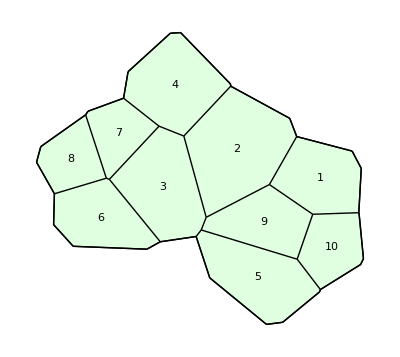

```mathematica
ShowTissue[w, "CellNumbers"-> True]
```

Determine the Connection List

```mathematica
ConnectionList[w]
```

{{1,2},{1,9},{1,10},{2,1},{2,3},{2,4},{2,9},{3,2},{3,4},{3,5},{3,6},{3,7},{3,9},{4,2},{4,3},{4,7},{5,3},{5,9},{5,10},{6,3},{6,7},{6,8},{7,3},{7,4},{7,6},{7,8},{8,6},{8,7},{9,1},{9,2},{9,3},{9,5},{9,10},{10,1},{10,5},{10,9}}

```mathematica
ConnectionList[w, "UpperTriangular"-> True]
```

{{1,2},{1,9},{1,10},{2,3},{2,4},{2,9},{3,4},{3,5},{3,6},{3,7},{3,9},{4,7},{5,9},{5,10},{6,7},{6,8},{7,8},{9,10}}

Now find the connection matrix.

```mathematica
ConnectionMatrix[w]
```

SparseArray[<36>,{10,10}]

```mathematica
MatrixForm[ConnectionMatrix[w]]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0)

```mathematica
MatrixForm[ConnectionMatrix[w, "UpperTriangular"-> True]]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)